## Supervised Learning: Prediction

Predict numerical values based on continuous variables - Example 1

```mathematica
trainingSet = {1->1.3,2->2.4,3->6.4,4->10.1}
```

{1→1.3,2→2.4,3→6.4,4→10.1}

```mathematica
p=Predict[trainingSet]
```

PredictorFunction[…]

```mathematica
p[1.5]
```

2.08415

```mathematica
dist = p[1.5,"Distribution"]
```

NormalDistribution[2.08415,1.05581]

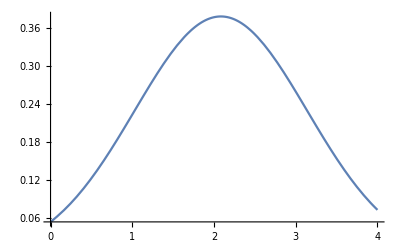

```mathematica
Plot[PDF[dist,x],{x,0,4}]
```

Predict numerical values based on continuous variables - Example 2

```mathematica
bhData = ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"];
```

```mathematica
RandomSample[bhData,1]
```

{{7.05042,0,18.1,0,0.614,6.103,85.1,2.0218,24,666,20.2,2.52,23.29}→13.4}

```mathematica
pBH = Predict[bhData]
```

PredictorFunction[…]

```mathematica
pm = PredictorMeasurements[pBH,ExampleData[{"MachineLearning","BostonHomes"},"TestData"]]
```

PredictorMeasurementsObject[…]

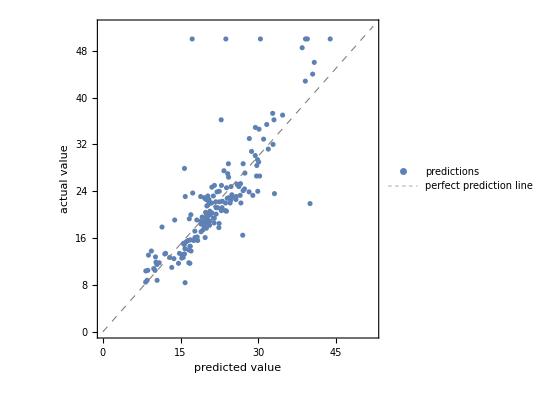

```mathematica
pm["ComparisonPlot"]
```

```mathematica
pm["StandardDeviation"]
```

5.17659

```mathematica
pm["Properties"]
```

{ComparisonPlot,InversePerplexity,Likelihood,LogLikelihood,LogLikelihoodRate,MeanDeviation,MeanSquare,Perplexity,Properties,RejectionRate,ResidualHistogram,ResidualPlot,Residuals,StandardDeviation,TotalSquare}

Predict numerical values based on continuous variables - Example 3

```mathematica
trainingSetAngular = Image[AngularGauge[#]]->#&/@RandomReal[1,100];
```

```mathematica
RandomSample[trainingSetAngular,3]
```

{-Graphics-→0.876075,-Graphics-→0.726959,-Graphics-→0.37353}

```mathematica
angularP = Predict[trainingSetAngular]
```

PredictorFunction[…]

```mathematica
Row[{
AngularGauge[Dynamic[t]],
Style["->",Large],
Dynamic[Labeled[AngularGauge[angularP[Image[AngularGauge[t]]]],"(Predicted value)"]]},
BaseStyle->FontFamily->"Sans Serif"]
```

->